```mathematica
a = 1; (*length side of triangle*)
triangle = {{0, 0},{a, 0}, {a/2, √(a^2-a^2/4)}};
Lines = {};
triangles = {triangle};
n = 8(*n > 3*)
iterations = 6 (2^(n-3)-1);
coef = 1/2;
```

8

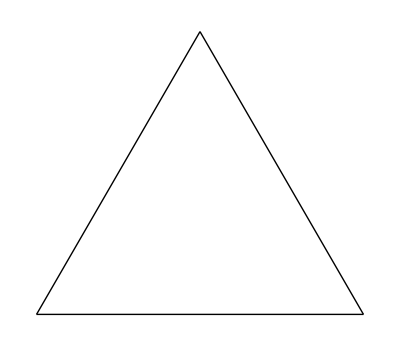

```mathematica
drawTriangle[tr_]:=
Graphics[{
Line[{tr[[1]],tr[[2]]}],
Line[{tr[[2]],tr[[3]]}],
Line[{tr[[3]],tr[[1]]}]}
];
drawTriangle[triangle]
```

```mathematica
newPointsFirst[tr_, k_]:=Module[
{point1, point2, point3, point4, point5, point6},
point1= tr[[1]]+k(tr[[1]]-tr[[3]]);
point2= tr[[1]]+k(tr[[1]]-tr[[2]]);
point3= tr[[2]]+ k(tr[[2]]-tr[[1]]);
point4 = tr[[2]]+k(tr[[2]]-tr[[3]]);
point5 = tr[[3]] + k (tr[[3]]-tr[[1]]);
point6= tr[[3]] + k (tr[[3]] - tr[[2]]);
{point1, point2, point3, point4, point5, point6}
];
```

```mathematica
addTrianglesFirst[tr_,k_]:=Module[
{points},
points = newPointsFirst[tr, k];
triangles = Join[triangles, {
{tr[[1]], points[[1]], points[[2]]},
{tr[[2]], points[[3]], points[[4]]},
{tr[[3]], points[[5]], points[[6]]}}];
];
```

```mathematica
newPoints[tr_, k_] := Module[
{point1, point2, point3, point4},
point1 = tr[[2]]+ k(tr[[2]]-tr[[1]]);
point2 = tr[[2]]+k(tr[[2]]-tr[[3]]);
point3 = tr[[3]] + k (tr[[3]]-tr[[1]]);
point4 = tr[[3]] + k (tr[[3]] - tr[[2]]);
{point1, point2, point3, point4}
];
```

```mathematica
addTriangles[tr_,k_]:=Module[
{points},
points = newPoints[tr, 1/2];
triangles = Join[triangles, {
{tr[[2]], points[[1]], points[[2]]},
{tr[[3]], points[[3]], points[[4]]}}];
];
```

```mathematica
addTrianglesFirst[triangle, coef];
triangles
coef = coef/2;
```

{{{0,0},{1,0},{1/2,(√3)/2}},{{0,0},{-1/4,-(√3)/4},{-1/2,0}},{{1,0},{3/2,0},{5/4,-(√3)/4}},{{1/2,(√3)/2},{3/4,(3 √3)/4},{1/4,(3 √3)/4}}}

```mathematica
drawTriangles := Show[Map[drawTriangle, triangles]];
```

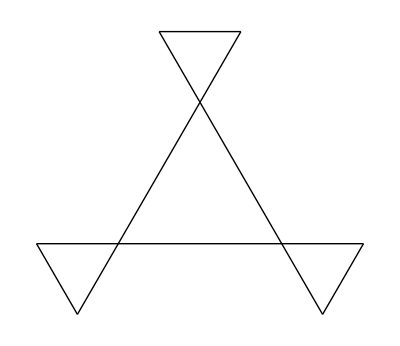

{{{0,0},{1,0},{1/2,(√3)/2}},{{0,0},{-1/4,-(√3)/4},{-1/2,0}},{{1,0},{3/2,0},{5/4,-(√3)/4}},{{1/2,(√3)/2},{3/4,(3 √3)/4},{1/4,(3 √3)/4}}}

```mathematica
drawTriangles
triangles
j = 2;
```

```mathematica
Do[Do[
addTriangles[triangles[[j]], coef];
j = j + 1,{k,1,3 2^(i-2)}];
coef =  coef /2,{i,2, n - 1}]
```

382

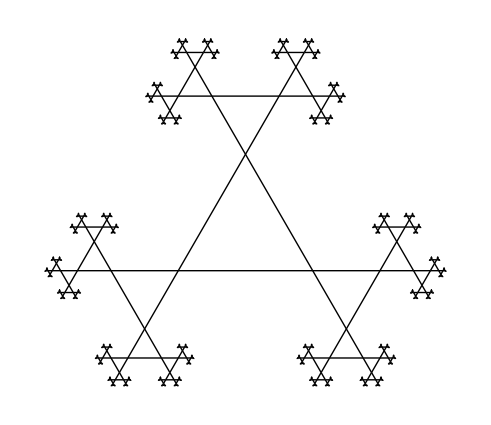

```mathematica
Length[triangles]
drawTriangles
```